```mathematica
V = 27.67
```

27.67

```mathematica
C1 = 1.584/(V)
```

0.0572461

```mathematica
k = 3.19/60+0.0078
```

0.0609667

ADC is for Average Droplet Concentration

```mathematica
ADC[x_]:=C1/k*(1-Exp[-k*x])
```

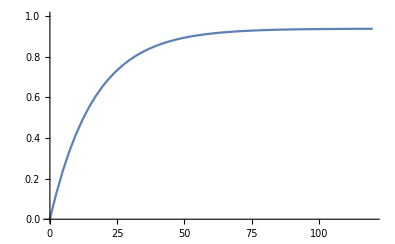

```mathematica
Plot[ADC[j],{j,0,120},PlotRange -> {{0,120},{0,1}}]
```

```mathematica
Manipulate[Plot[(C1/k*(1-Exp[-k*j])),{j,0,120},PlotRange -> {{0,120},{0,10}}],{k,0,1}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Manipulate[Plot[(0.6*(1-Exp[-(C1/k*(1-Exp[-k*j]))/k+C1*j])),{j,0,120},PlotRange -> {{0,120},{0,1}}],{k,0,0.1}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Manipulate[Plot[(Factorial[3]/(Factorial[2]*Factorial[1]))*(0.6*(1-Exp[-(C1/k*(1-Exp[-k*j]))/k+C1*j]))^1*(1-(0.6*(1-Exp[-(C1/k*(1-Exp[-k*j]))/k+C1*j])))^2,{j,0,120},PlotRange -> {{0,20},{0,1}}],{k,0,0.1}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.